```mathematica
dir="D:\\better output 2";
```

```mathematica
dir="D:\\betterOutput";
```

```mathematica
GetNumberOfOrganisms[frameNo_]:=Module[{path,i,items,nOrganisms},
path = StringForm["``\\output\\frame``.json",dir,frameNo];
{i}=Import[path//ToString];
items = "Items"/.i;
nOrganisms="o"/.items//CountDistinct;
nOrganisms
]
```

```mathematica
f0=0;
fMax=5557110;
df=10000;
frames=Table[f,{f,f0,fMax,df}];
nOrgsList=ParallelMap[GetNumberOfOrganisms,frames];
```

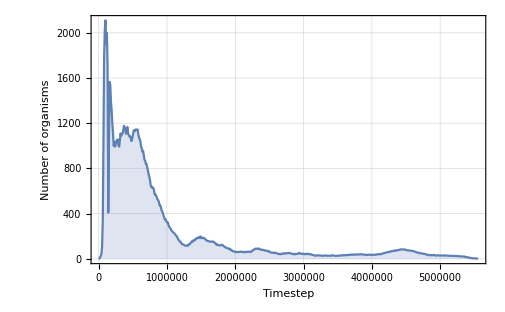

```mathematica
ListPlot[
nOrgsList,
DataRange->{f0,fMax},
Filling->Bottom,
Joined->True,
PlotRange->Full,
Frame->{{True,False},{True,False}},
FrameLabel->{"Timestep","Number of organisms"},
GridLines->Automatic
]
```